# Non Dual Unitary Circuit from a 13-dimensional C*-WHA A_Fib

## Constructing the tensors from algebraic data

```mathematica
(*Load algebraic data from file; here R is the universal R-matrix which is not useful for this project*)
SetDirectory[NotebookDirectory[]];
<<HAQCATools`;<<HATools`;<<TensorTools`;
HAName="Fibonacci";
{mul,Δ, η, ϵ, S, R, Rb}=LoadHA[HAName];{RepNames,CorepNames}
```

{{ρ2Map,ρ3Map},{V2,V3}}

```mathematica
(*Verify weak Hopf algebra axioms*) 
VerifyWHAAxioms[mul,Δ,η,ϵ,S]
```

True

```mathematica
(*Check representation and corepresentation of Subscript[A, Fib]*)
{CheckRep[ρ3Map,mul,η],CheckCorep[V3,Δ,ϵ]}//FullSimplify
```

{True,True}

```mathematica
(*Cosntruct {Ugate,ρRTensor,vRTensor,ηTensor,ϵTensor} using algebraic data via Eq.(2), and ρLTensor,vLTensor Via Eq.(E13). (ρLTensor,vLTensor are not used in this code)*) 
{Ugate,ρLTensor,ρRTensor,vLTensor,vRTensor,ηTensor,ϵTensor}=QCATensors[mul,Δ, η, ϵ, S, SparseArray@ρ3Map,SparseArray@ V3];
```

```mathematica
(*Verify the first line of Eq.(1)*)
VerifyPentagon[Ugate,ρLTensor,ρRTensor,vLTensor,vRTensor,ηTensor,ϵTensor]//FullSimplify
```

{True,True}

```mathematica
(*Verify the second line of Eq.(1). Then verifies the other 3 equations in Eq.(A20). Note that since Subscript[A, Fib] is only a WHA, only the latter is satisfied.*)
VerifyBoundaryηϵ[Ugate,ρLTensor,ρRTensor,vLTensor,vRTensor,ηTensor,ϵTensor]//FullSimplify
```

{False,True}

## Compute local observables and correlations in quench dynamics

```mathematica
(*Prepare for numerical computations*)
 ϕ=N[(1+√5)/2];
ζ=1/√ϕ;Id=IdentityMatrix;{Ugate,ρLTensor,ρRTensor,vLTensor,vRTensor,ηTensor,ϵTensor}=N[{Ugate,ρLTensor,ρRTensor,vLTensor,vRTensor,ηTensor,ϵTensor}];
(*Use the following lines for better precision:*)
(*$MinPrecision=40;
ϕ=N[(1+√5)/2,40];
ζ=1/√ϕ;{Ugate,ρLTensor,ρRTensor,vLTensor,vRTensor,ηTensor,ϵTensor}=N[QCATensors[mul,Δ, η, ϵ, S, SparseArray@ρ3Map,SparseArray@ V3],40];*)
```

```mathematica
(*Define the initial product state*)
Ψ33=N[SparseArray/@ProductStateMPS[{0,0,1},{0,0,1}]];
(*for better precision: *)
(*Ψ33=N[SparseArray/@ProductStateMPS[{0,0,1},{0,0,1}],40];*)
{χL,χR,ψρ,ψv}=Ψ33;
```

```mathematica
(*Define local observables and correlations functions to compute in quench dynamics*)
Corr33[A_,B_,x_,t_]:=Corr[A,B,Ψ33,x,t,ρRTensor,vRTensor,ηTensor,ϵTensor];
Observable33[A_,t_]:=If[Mod[2t,2]==0,Corr33[A,Id[3],0,t],Corr33[Id[3],A,0,t]];
O32[t_]:=If[Mod[2t,2]==0,Corr33[el[3,3,3],el[2,2,3],0,t],Corr33[el[3,3,3],el[2,2,3],0,t+1/2]];
O3321[t_]:=If[Mod[2t,2]==0,2Re[Corr33[el[3,2,3],el[3,1,3],0,t]],
2 ζ^3 Corr33[el[2,2,3],el[1,1,3],0,t+1/2]-2 ζ^3 Corr33[el[3,3,3],el[3,3,3],0,t+1/2]+2 ζ^6 Re@Corr33[el[3,2,3],el[3,1,3],0,t+1/2]
];
```

```mathematica
<<MaTeX`;
```

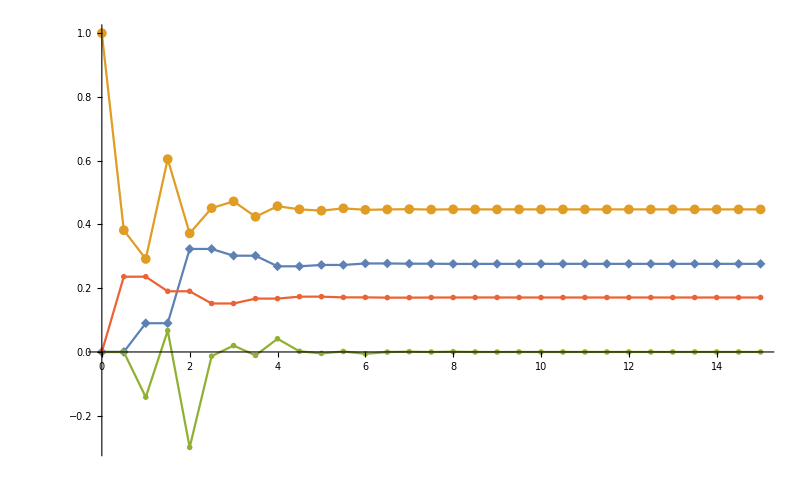

```mathematica
(*Reproduce Fig.3*)
DiscretePlot[{Observable33[el[2,2,3],t],Observable33[el[3,3,3],t],O3321[t],O32[t]},{t,0,15,1/2},PlotRange->All,PlotLegends->Placed[LineLegend[{MaTeX["\\hat{O}=|2\\rangle\\langle 2|",Magnification->2],MaTeX["\\hat{O}=|3\\rangle\\langle 3|",Magnification->2],MaTeX["\\hat{O}=|33\\rangle\\langle 21|+h.c.",Magnification->2],MaTeX["\\hat{O}=|32\\rangle\\langle 32|",Magnification->2]},LegendFunction->Framed],{0.8,0.79}], AxesLabel->{MaTeX["t",Magnification->2.5],MaTeX["\\langle\\hat{O}(t)\\rangle",Magnification->2.5]}, 
TicksStyle->Directive[Black, Thick,22],
Filling->None,
Joined->True,
(*PlotMarkers->None,*)
(*PlotMarkers->{"▲","■"},*)
PlotMarkers->{"◆","●","▶","◀"},
AxesStyle->AbsoluteThickness[3]]
```

```mathematica
(*Plot correlation function W^ij(x,t) defined in Eq.(69)*)
WPlot[i_,j_,xRange_]:=Module[{W,WData},
(*W[x_,t_]:=If[x>2t,0,Corr33[el[i,i,3],el[j,j,3],x,t]-Corr33[el[i,i,3],Id[3],x,t]*Corr33[Id[3],el[j,j,3],x,t]];*)
W[x_,t_]:=Corr33[el[i,i,3],el[j,j,3],x,t]-Corr33[el[i,i,3],Id[3],x,t]*Corr33[Id[3],el[j,j,3],x,t];
WData =Table[{x,t,W[x,t]},{x,0,xRange},{t,0,xRange/2}];
MatrixPlot[Reverse@WData[[All,All,3]],
AspectRatio->1,
DataRange->{{0,xRange/2},{0,xRange}},
FrameLabel->{MaTeX["x",Magnification->2.5],MaTeX["t",Magnification->2.5]}, 
FrameTicksStyle->Directive[Black, Thick,20],
FrameStyle->AbsoluteThickness[2.5],
DataReversed->True]];
```

Power::indet: Indeterminate expression 0^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

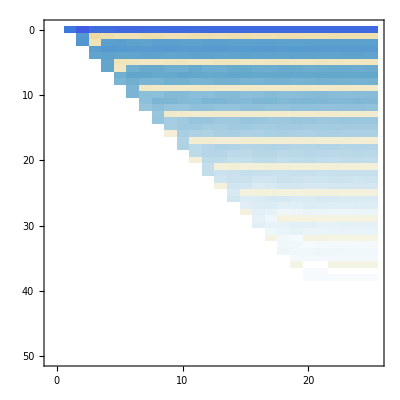

```mathematica
(*Reproduce Fig.4*)
(*Note: to exactly reproduce Fig.4, one need to use higher numerical precisions in earlier steps*)
WPlot[2,2,50]
```

## Compute Renyi Entanglement entropy in quench dynamics

```mathematica
(*Compute the transfer matrices needed for Renyi entanglement entropy calculations*)
(*$MinPrecision=$MachinePrecision;*)
 TMs=TMRenyiSmallSystemLargeα[SparseArray/@Ψ33,ρRTensor,vRTensor,ηTensor,ϵTensor];
```

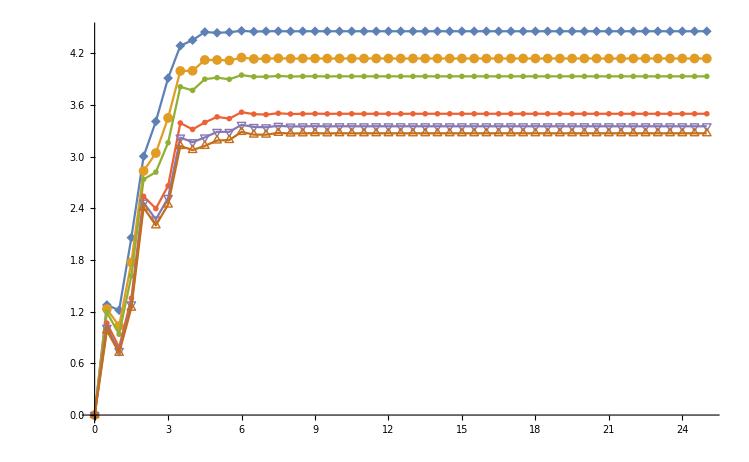

```mathematica
(*Compute the Renyi Entanglement entropy for small subsystem, and reproduce the first plot in Fig.5.*)
RenyiFinSubsEven[L_,t_,α_]:=RenyiSmallSystemLargeα[α,L,t,TMs];DiscretePlot[{RenyiFinSubsEven[5,t,2],RenyiFinSubsEven[5,t,3],RenyiFinSubsEven[5,t,4],RenyiFinSubsEven[5,t,10],RenyiFinSubsEven[5,t,20],RenyiFinSubsEven[5,t,50]},{t,0,25,1/2},
PlotLegends->Placed[LineLegend[{MaTeX["\\alpha=2",Magnification->2],MaTeX["\\alpha=3",Magnification->2],MaTeX["\\alpha=4",Magnification->2],MaTeX["\\alpha=10",Magnification->2],MaTeX["\\alpha=20",Magnification->2],MaTeX["\\alpha=50",Magnification->2]},LegendFunction->Framed],{0.8,0.4}], AxesLabel->{MaTeX["t",Magnification->2.5],MaTeX["H_\\alpha[\\hat{\\rho}_A(t)]",Magnification->2.5]}, 
TicksStyle->Directive[Black, Thick,22],
Filling->None,
Joined->True,
PlotMarkers->{"◆","●","▶","◀","▽","△"},
AxesStyle->AbsoluteThickness[3]]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

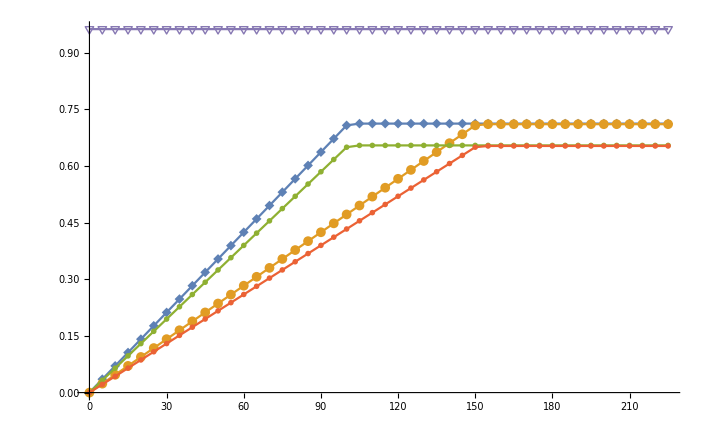

```mathematica
(*Compute the Renyi Entanglement entropy for large subsystem and small index α, and reproduce the second plot in Fig.5. This may take up to an hour*)
Needs["PlotLegends`"];<<MaTeX`;MaxEE[n_]:=N[Log[Fibonacci[n+3]]];
RenyiFin[L_,t_,α_]:=RenyiFiniteSystemSmallα[α,L,t,Ψ33,ρRTensor,vRTensor,ηTensor,ϵTensor];
DiscretePlot[{RenyiFin[200,t,2]/200,RenyiFin[300,t,2]/300,RenyiFin[200,t,3]/200,RenyiFin[300,t,3]/300,2Log[ϕ]//N},{t,0,225,5},
PlotLegends->Placed[LineLegend[{MaTeX["\\alpha=2,L_A=200",Magnification->2],MaTeX["\\alpha=2,L_A=300",Magnification->2],MaTeX["\\alpha=3,L_A=200",Magnification->2],MaTeX["\\alpha=3,L_A=300",Magnification->2],MaTeX["\\text{Max value}",Magnification->2]},LegendFunction->Framed],{0.8,0.35}], AxesLabel->{MaTeX["t",Magnification->2.5],MaTeX["H_\\alpha[\\hat{\\rho}_A(t)]/L_A",Magnification->2.5]}, 
TicksStyle->Directive[Black, Thick,22],
Filling->None,
Joined->True,

PlotMarkers->{"◆","●","▶","◀","▽","△"},
AxesStyle->AbsoluteThickness[3]]
```

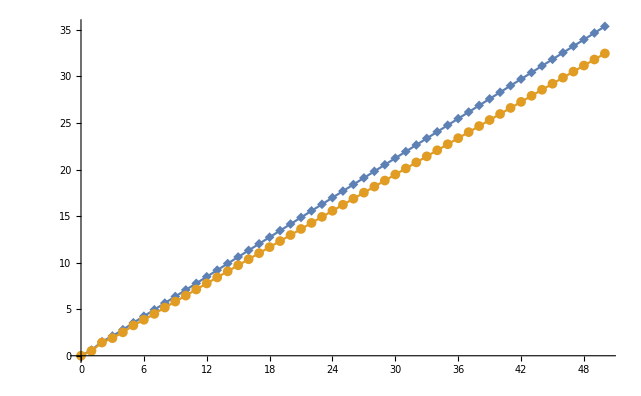

```mathematica
(*Compute the Renyi Entanglement entropy for a semiinfinite half chain, and reproduce the last plot in Fig.5.*)Renyi[t_,α_]:=Renyi[t,α]=RenyiSemifinite[α,t,Ψ33,ρRTensor,vRTensor,ηTensor,ϵTensor];
DiscretePlot[{Renyi[t,2],Renyi[t,3]},{t,0,50,1},
PlotLegends->Placed[LineLegend[{MaTeX["\\alpha=2",Magnification->2],MaTeX["\\alpha=3",Magnification->2]},LegendFunction->Framed],{0.2,0.8}], AxesLabel->{MaTeX["t",Magnification->2.5],MaTeX["H_\\alpha[\\hat{\\rho}_A(t)]",Magnification->2.5]}, 
TicksStyle->Directive[Black, Thick,22],
Filling->None,
Joined->True,
(*PlotMarkers->None,*)
(*PlotMarkers->{"▲","■"},*)
PlotMarkers->{"◆","●"},
AxesStyle->AbsoluteThickness[3]]
```

## Verify finite system revival time

```mathematica
(*We first compute the order of the weak Hopf algebra Subscript[A, Fib]. Define the faithful 5-dimensional representation ρfund and corepresentation vfund using direct sum of all irreps*) 
ρfund=DirectSum[ρ2Map,ρ3Map]; vfund=DirectSum[V2,V3];{CheckRep[ρfund,mul,η],CheckCorep[vfund,Δ,ϵ]//FullSimplify}
```

{True,True}

```mathematica
(*Apply ρfund and vfund to the canonical element via Eq.(A36)*) 
CEfund=Π[5].First[QCATensors[mul,Δ, η, ϵ, S, SparseArray@ρfund,SparseArray@vfund]];
(*The order of the canonical element is equal to its order in any faithful representation, and here we compute it in the representation ρ⊗v.*) 
Table[MatrixPower[CEfund,k]==MatrixPower[CEfund,2],{k,3,11}]//FullSimplify
```

{False,False,False,False,True,False,False,False,False}

```mathematica
(*So we conclude that the canonical element has order n=5*)
MatrixPower[CEfund,2]==MatrixPower[CEfund,7]//FullSimplify
```

True

```mathematica
(*Now compute numerically the revival time for small system sizes L=2,3,4*)
{U2PBC,U3PBC,U4PBC}=First[PBCEvol[Ugate,#]]&/@{2,3,4};
```

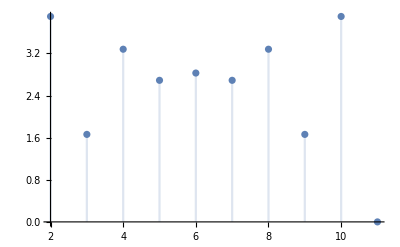

```mathematica
(*For L=2, revival time is n L=10*)
DiscretePlot[Norm[MatrixPower[U2PBC,k]-U2PBC,"Frobenius"],{k,2,11}]
```

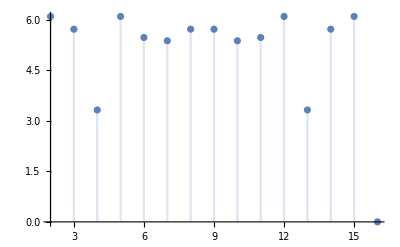

```mathematica
(*For L=3, revival time is n L=15*)
DiscretePlot[Norm[MatrixPower[U3PBC,k]-U3PBC,"Frobenius"],{k,2,16}]
```

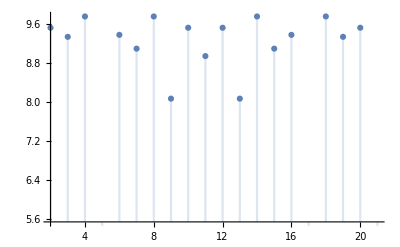

```mathematica
(*For L=4, revival time is n L=20*)
DiscretePlot[Norm[MatrixPower[U4PBC,k]-U4PBC,"Frobenius"],{k,2,21}]
```